results for

prec = 32 
 steps = 100
 order = 8

Norm[expr, p] with p=2

GammaApprox[y] =  1-0.57718153727232845179923701371244 y+0.98800245952493279785280576726774 y^2-0.89558754591886619241853393249838 y^3+0.91301170264207281775293611206471 y^4-0.74669048148554992630338867126929 y^5+0.47145947686199270062620914103596 y^6-0.18750688878401224646677217819982 y^7+0.034492814431758500755980775312 y^8

log10MaxError -6.460406627072502315475714692

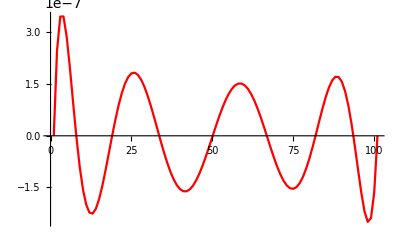

Norm[expr, p] with p=Infinity

GammaApprox[y] =  1-0.57719163253966214521880372612658 y+0.98820652326977805872648131605862 y^2-0.89706896211793777507370423730764 y^3+0.91827658514210061170000379125263 y^4-0.75689378485537851129214514261739 y^5+0.48246621650392149500431384972904 y^6-0.19371557688307775775501630547528 y^7+0.035920631480256023908870454487 y^8

log10MaxError -6.668217054109154587606329

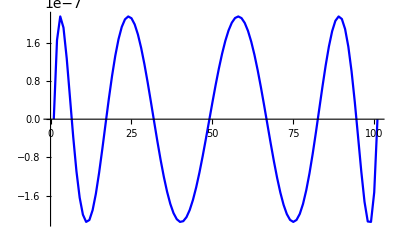

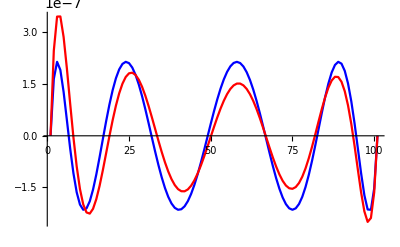

max Memory used 0.100685 GB

elapsed time 0.8808435 sec

1-(307795722978842 x)/533273680986813+(61715670962370110 x^2)/62465098510023173-(1402957953342009 x^3)/1566522401673847+(10903440957362298 x^4)/11942279519320427-(5767174995407986 x^5)/7723648738543071+(13583032766929699 x^6)/28810605011776596-(385709861673796 x^7)/2057043686102073+(135471455528618 x^8)/3927526870752699-Gamma[1+x]

{x→0.0695434}

{x→0.180314}

{x→0.325787}

{x→0.491014}

{x→0.658169}

{x→0.80867}

{x→0.925538}

1-(13918955835996938 x)/24114964686430181+(4276150119326539 x^2)/4327182647183518-(5301100690934987 x^3)/5909356933294556+(8785579175343835 x^4)/9567465094391242-(3285262402316029 x^5)/4340453664768501+(4311794541914452 x^6)/8936987491391339-(1942243205468823 x^7)/10026262403467513+(164519203163618 x^8)/4580075471502969-Gamma[1+x]

{x→0.0554592}

{x→0.161859}

{x→0.308801}

{x→0.480823}

{x→0.657237}

{x→0.815712}

{x→0.935049}

```mathematica
(*Input precision,number of steps,polynomial oder*)
prec=32;steps=100;order=8;
(*start time of code execution*)
start=AbsoluteTime[];
(*polynomial components*)
w=(y^#&)/@Range[order-1];
parms=(Symbol["a"<>ToString[#]]&)/@Range[order-1];
(*data generation*)
f[y_]=Gamma[1+y];
model[y_]=1+Total[parms w]-Total[parms] y^order;
data=({#,f[#]}&)/@Range[0,1,1/steps];

(*main procedure fitting the coefficients*)
getApprox[params_,data_,f_,model_,norm_]:=
Module[{x,coeffs},coeffs=FindFit[data,model[x],params,x,
NormFunction->(Norm[#,norm]&),
WorkingPrecision->prec];
Return[coeffs];];

(*verification procedure get differences*)
verify[coeffs_,data_,f_,model_,norm_]:=
Module[{x,n,diffs,title,logMax10Error},
n=Length[data]-1;
title="Norm[expr, p] with p="<>ToString[norm];
diffs=(model[#]-f[#]/.coeffs&)/@Range[0,1,1/n];
logMax10Error=N[Log10[Max[Abs[diffs]]],prec];
Print[title];
Print["GammaApprox[y] =  ",model[y]/.coeffs];
Print["log10MaxError ",logMax10Error];
Return[diffs];];

(*start main*)
Print["results for"];
Print[" prec = ",prec "\n steps = ",steps,"\n order = ",order];
(*least square norm*)
c2=getApprox[parms,data,f,model,norm=2];
d2=verify[c2,data,f,model,norm=2];
h2=ListPlot[d2,Joined->True,PlotStyle->Red]
(*supremum norm*)
lst = CoefficientList[model[z]/.c2,z] ;
p2=({parms[[#]],lst[[#+1]]}&)/@Range[1,order-1];

ci=getApprox[p2,data,f,model,norm=Infinity];
di=verify[ci,data,f,model,norm=Infinity];
hi=ListPlot[di,Joined->True,PlotStyle->Blue]
(*graphics*)
Show[{hi,h2},PlotRange->All]
(* print statistics *)
stop=AbsoluteTime[];
Print["max Memory used ",1.0*10^(-9) MaxMemoryUsed[]," GB"]
Print["elapsed time ",stop-start," sec"]

dif[x_]=Rationalize[model[x]-f[x]/.c2, 10^-prec]
FindRoot[dif[x]==0,{x,7/100}]
FindRoot[dif[x]==0,{x,18/100}]
FindRoot[dif[x]==0,{x,35/100}]
FindRoot[dif[x]==0,{x,50/100}]
FindRoot[dif[x]==0,{x,67/100}]
FindRoot[dif[x]==0,{x,82/100}]
FindRoot[dif[x]==0,{x,93/100}]

dif[x_]=Rationalize[model[x]-f[x]/.ci, 10^-prec]
FindRoot[dif[x]==0,{x,7/100}]
FindRoot[dif[x]==0,{x,18/100}]
FindRoot[dif[x]==0,{x,35/100}]
FindRoot[dif[x]==0,{x,50/100}]
FindRoot[dif[x]==0,{x,67/100}]
FindRoot[dif[x]==0,{x,82/100}]
FindRoot[dif[x]==0,{x,93/100}]
```